## 3.029 Spring 2022 Lecture 06 - 02/16/2022

## Legendre Transformations

Last lecture, we introduced the concept of Legendre transforms as a way of “changing variables” from one thermodynamic potential to another

We did so by a rather prescribed process, namely:

Define a new thermodynamic potential,                    Φ = U - Y X

Take its total differential,                                               dΦ = dU - Y dX - X dY

Use the fundamental thermodynamic relation,  dU = T dS - P dV

Simplify expression

As a reminder, the key thermodynamic potentials we defined this way are:

Internal Energy,	                               dU(S,V) = T dS - P dV

Entropy,                                               dS(U,V) = 1/T dU + P/T dV

Enthalpy,                                             dH(S,P) = T dS + V dP

Helmholtz Free Energy,                 dA(T,V) = -S dT - P dV

Gibbs Free Energy,                           dG(T,P) = -S dT + V dP

Note: This procedure is not restricted to named potentials. If you have other work terms in your potential, 

e.g. electrical work in an dielectric medium, ℰ 𝒫, where ℰ is the (intensive) internal electric field, and 𝒫 is the (extensive) total polarization,
then the fundamental thermodynamic relation would read: d U = T dS - P dV + ℰ d𝒫 (remember, the variations are wrt extensive variables),

and we want to instead express this in terms of the internal electric field, we would define:

  Φ  = U - ℰ 𝒫
dΦ = d U - ℰ d𝒫  - 𝒫 dℰ
dΦ = T dS - 𝒫 dℰ

This is largely all you will need in your thermodynamics and statistical mechanics courses

But in this lecture, we will go a step further, and provide an intuitive geometrical picture of what the Legendre transform does

## Convex Functions

The Legendre transform is defined for general functions, but it is particularly useful in looking at convex functions

What exactly is a convex function?

For a univariate function, f(x), if you pick any two points, x_1 and x_2
convexity implies that for every point in the interval between x_1 and x_2

(which we’ll define parametrically as x(t)=x_1+t[f(x_2)-f(x_1)] for 0< t <1)

then we must obey: f(x(t)) > f(x_1) + t(f(x_2)-f(x_1))

Let’s visualize this!

An important thing to note about convexity is that it is not local:
 the construction depends on geometry that is not in the proximity of the point (x,f[x])

This turns out to be important when we think about the convexity of thermodynamic potentials

Suppose that U[x] is the internal energy of a system with a fixed number of moles—for example, if there is one mole, then we can call  the molar internal energy.

Suppose further that x is the molar density of some extensive quantity. In our system, let’s suppose that x is the molar volume .  Then  is the molar energy as a function of the molar volume.

1) If   is not convex then we can find two other molar volumes   and  (for example, molar volumes of 1/2 and and 3/4)  such that the system’s average value is    is between  and  (for example if    = 5/8, then half of the system is at   and the other half is at )

If    is not convex, the system can lower its molar internal energy by separating into a dense and less dense portion such that the average molar volume remains constant

-Graphics-

If however,   is convex, there are no two other molar volumes for which the energy is lower 

-Graphics-

### Convexity in higher dimensions

In the examples above, we were considering the convexity of a graph .

The definition we used above for convexity can be generalized to higher dimensions, but it becomes less intuitive

Instead, we will consider what “non-convexity” means to get a better intuition:

Let’s consider the a 2D surface embedded in 3D dimensions parametrically:
{x[u,v], y[u,v], z[u,v]}

Spheres and ellipsoids are convex surfaces

```mathematica
convexShape=Module[{f},
f[u_,v_]:={Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]};

ParametricPlot3D[f[u,v],{u,0,Pi},{v,-Pi,Pi}]//Rasterize
]
```

-Graphics-

By contrast, this is a not convex surface

```mathematica
nonConvexShape=Module[{f},
f[u_,v_]:=(1- Cos[4 u]/8){Cos[u]Cos[v],Sin[u]Cos[v],Cos[v]Sin[v]};

ParametricPlot3D[f[u,v],{u,0,Pi},{v,-Pi,Pi}]//Rasterize
]
```

-Graphics-

“Non-convexity” mean that:
for any point {x,y,z} on the surface, there are other points that can be connected with a hyperplane (the higher-dimensional generalization of a line) and have part of the plane be “outside” the surface.

Convexity means there are no other such points.

We can “convexify” regions by constructing a convex hull

We will revisit the concept of a Convex Hull many times during our course!

For now, we note that it’s a convex envelope which includes all points on our shape, and satisfies the convexity criterion above

```mathematica
Block[{nonConvexRegion,ch,points},
nonConvexRegion=ParametricRegion[(1- Cos[4 u]/8){Cos[u]Cos[v],Sin[u]Cos[v],Cos[v]Sin[v]},{{u,0,Pi},{v,-Pi,Pi}}];
points=RandomPoint[nonConvexRegion,10000];
ch = ConvexHullMesh[points,MeshCellStyle->{{2,All}->Opacity[0.25]}];

GraphicsRow[{Graphics3D[Point[points],Boxed->False],ch,Show[ch,nonConvexShape]},ImageSize->750]//Rasterize

]
```

-Graphics-

Such “convexification” is what one would use if the molar internal energy were a function of two molar variables

Another very important application of convex functions in Materials Science, is in constructing equilibrium crystal shapes based on the surface energy per unit are of different crystal orientations

We will investigate this later in the course!

## Geometric Interpretation

Now that we understand convex functions, let’s go back to our Legendre transform and start by looking at a convex function in a single variable

```mathematica
convex[x_]=x Log[x]
```

x Log[x]

We can use the built-in FunctionConvexity to ensure the function is indeed convex

```mathematica
FunctionConvexity[x Log[x],x]
```

Indeterminate

This is because Log of a negative number is complex-valued.
We will restrict our range between 0-1 for now

```mathematica
FunctionConvexity[{x Log[x],1>= x>= 0},x]
```

1

Of-course an easier way would be to just plot it!

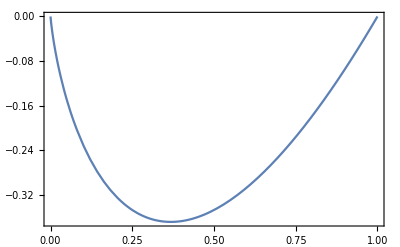

```mathematica
Plot[convex[x],{x,0,1},Frame->True]
```

We will now treat this as a “cup” and fill the inside of it

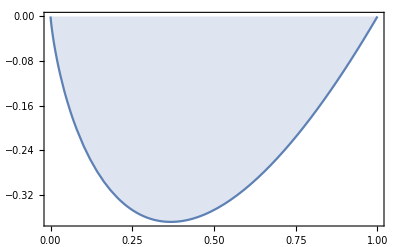

```mathematica
Plot[convex[x],{x,0,1},Frame->True,Filling->Top]
```

Mathematically, this is defined as the epigraph of a function f 
{{x,z} | z 	≥ f(x)}

```mathematica
convexEpigraph[x_,z_]=ImplicitRegion[convex[x]≤z,{{x,0,1},z}]
```

ImplicitRegion[Log[x] x≤z&&0≤x≤1,{x,z}]

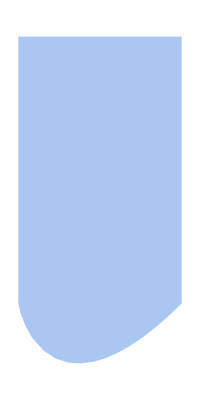

```mathematica
Region[convexEpigraph[x,z],PlotRange->{Automatic,{Automatic,0}}]
```

```mathematica
ConvexRegionQ[convexEpigraph[x,z]]
```

True

It’s easy to notice that the epigraph of a convex function forms a convex set

We now want to do the following:

Start way down below our epigraph

Make a straight line (y = m x + c) with some slope m such that it does not intersect the epigraph

and start moving it towards the epigraph (increasing c) until it touches

record the values (m,c)

```mathematica
Manipulate[
Plot[{convex[x],m x +c},{x,0,1},Frame->True,Filling->{1->Top}],
{{m,-1,"Slope"},-1,1},{{c,-2,"Intercept"},-2,4},
Paneled->False,SaveDefinitions->True]
```

For a given slope, m, there’s (at-most) one value of the intercept c that:

intersects the epigraph

and the entire epigraph is contained on just one side of the line

If we now graph these c vs m, we will obtain a concave function

Let’s check this for a few values

```mathematica
eyeballingPointsFromManipulate={{-0.925,-0.15},{-0.45,-0.23},{-0.15,-0.32},{0.015,-0.38},{0.33,-0.51},{0.605,-0.68}};
```

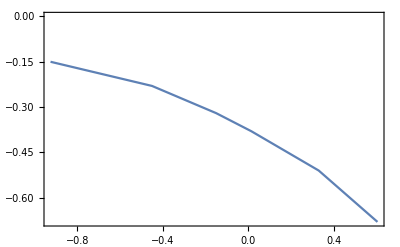

```mathematica
ListLinePlot[eyeballingPointsFromManipulate,Frame->True]
```

That means if we instead plot -c vs m, we obtain a convex function

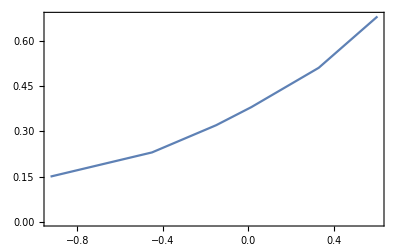

```mathematica
ListLinePlot[MapAt[-#&,eyeballingPointsFromManipulate,{All,2}],Frame->True]
```

This means  we can define a new function which takes the slope m as argument
and constructs the supporting hyperplanes of the epigraph of f

h(m) = -c

This new function h is the Legendre transform of f!

Let’s try and see if we can find an explicit expression for the Legendre transform

Note that our approach of trying to draw the the supporting hyperplanes of the epigraph of a function is similar to drawing envelopes of curves

This is also very related to the surface-energy construction we’ll see later!

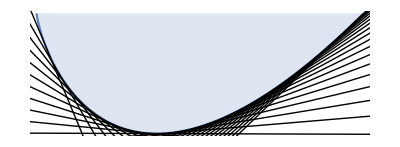

```mathematica
With[{n=30},
Show[
Graphics[{Thin,
Table[InfiniteLine[{t,convex[t]},{1,convex'[t]}],
{t,Rest@Most@Subdivide[n]}]}],
Plot[convex[x],{x,0,1},Frame->True,Filling->Top]]]
```

We are therefore looking for an x such that the point {x, m x - h(m)}  on the supporting hyperplane y = m x - h(m) belongs to f

Let’s perturb the slope slightly to obtain another hyperplane
y = (m+ϵ) x - h(m + ϵ)

This perturbed hyperplane intersects the original hyperplane at point
x = 1/ϵ[h(m + ϵ)-h(m)]

As we take the limit of ϵ→∞ this approaches the derivative h’(m)

As such the point
{ h’(m), m h’(m) - h(m) } lies on the graph of f for all m

We can express the derivative m at point x_0 as f'(x_0), and thus
{m, m x_0 - y_0} = {f'(x_0), x_0 f'(x_0) - f(x_0)} lies on the graph of h

This means that going from f to h and h to f have exactly the same form

The Legendre transform is its own inverse!

Let’s write a function to do this

First, we need to define our new variable
m = f’(x) and invert this equation to get an expression for x(m)

```mathematica
functionInTermsOfDerivative[f_][x_,m_]:=x/.First[Solve[m==f'[x],x,Assumptions->m∈Reals]]/.C[_]:>0
```

And then we can use this to evaluate our Legendre transform as
h(m) = x(m) m - f[x(m)]

```mathematica
naiveLegendreTransform[f_][x_Symbol,m_Symbol]:=Block[{xInTermsofM},
xInTermsofM[m]=functionInTermsOfDerivative[f][x,m];
FullSimplify[xInTermsofM[m] m - f[xInTermsofM[m]],Assumptions->m∈Reals]
]
```

```mathematica
convexLegendre[m_]=naiveLegendreTransform[convex][x,m]
```

ⅇ^(-1+m)

```mathematica
naiveLegendreTransform[convexLegendre][m,x]
```

x Log[x]

In-fact we can combine these steps in one Solve function

```mathematica
legendreTransform[f_][x_Symbol,m_Symbol]:=First[h/. Quiet[
Solve[h==x f'[x]-f[x]&&m==f'[x],
{x,h}],{Solve::incnst,Solve::ifun}]]
```

```mathematica
DynamicModule[{function,legendre,slope,intercept,x,m},

function[x_]=convex[x];
legendre[m_]=legendreTransform[convex][x,m];

Manipulate[

slope=function'[x0];
intercept=-legendre[slope];

GraphicsRow[{
Plot[function[x],{x,0,1},PlotLabel->function["x"],Frame->True,ImageSize->400,BaseStyle->14,PlotStyle->Directive[Blue,Thick],Epilog->{PointSize[0.025],Point[{x0,function[x0]}],InfiniteLine[{{x0,function[x0]},{0,intercept}}]}],

Plot[legendre[m],{m,-3,1},PlotLabel->legendre["m"],PlotStyle->Directive[Red,Thick],Frame->True,ImageSize->400,BaseStyle->14,Epilog->{PointSize[0.025],Point[{slope,-intercept}],Line[{{slope,-intercept},{slope,0}}]}]
},ImageSize->850
],{{x0,0.5},10^-6,1},Paneled->False,SaveDefinitions->True
]
]
```

This generalizes nicely to higher dimensions

```mathematica
legendreTransform[f_][x_List,m_List]:=First[h/. Quiet[
Solve[h==x.Grad[f@@x,x]-f@@x&&m==Grad[f@@x,x],
Append[x,h]],{Solve::incnst,Solve::ifun}]]
```

```mathematica
kineticEnergy[v1_,v2_]=1/2 m (v1^2+v2^2);
legendreTransform[kineticEnergy][{v1,v2},{p1,p2}]
```

(p1^2+p2^2)/(2 m)

## Physical Systems

Like the simple multidimensional example above shows the Lagrangian ↔ Hamiltonian transformations we did early in the class,
are in-fact common applications of Legendre transforms!

This can be seen by our definition of the canonical momentum

Since the Lagrangian L is a function of the time derivative of the generalized coordinates, 
and we’re using its derivative to introduce a new “variable” in the Hamiltonian

Let’s see if we can use our general function above to do the transformation for the double pendulum we saw in the second lecture

```mathematica
lagrangian[θ1Prime_,θ2Prime_]=-g (Cos[θ[2][t]] l[2] m[2]+Cos[θ[1][t]] l[1] (m[1]+m[2]))+1/2 (l[1]^2 (m[1]+m[2]) (θ[1]'[t])^2+2 Cos[θ[1][t]-θ[2][t]] l[1] l[2] m[2] θ[1]'[t] θ[2]'[t]+l[2]^2 m[2] (θ[2]'[t])^2)/.{θ[1]'[t]->θ1Prime,θ[2]'[t]->θ2Prime,θ[1][t]->q1,θ[2][t]->q2};
```

```mathematica
Simplify[legendreTransform[lagrangian][{θ1Prime,θ2Prime},{p1,p2}]]
```

-((p2^2 l[1]^2 m[1]+p2^2 l[1]^2 m[2]-2 p1 p2 Cos[q1-q2] l[1] l[2] m[2]+p1^2 l[2]^2 m[2]+2 g Cos[q2] l[1]^2 l[2]^3 m[1] m[2]^2+2 g Cos[q2] l[1]^2 l[2]^3 m[2]^3+2 g Cos[q1] l[1]^3 l[2]^2 m[2] (m[1]+m[2])^2-2 g Cos[q1-q2]^2 l[1]^2 l[2]^2 m[2]^2 (Cos[q2] l[2] m[2]+Cos[q1] l[1] (m[1]+m[2])))/(l[1]^2 l[2]^2 m[2] (-2 m[1]-m[2]+Cos[2 (q1-q2)] m[2])))

Which is indeed the expression we derived in lecture 2!

Note: above we defined the lagrangian as only a function of the derivatives of the generalized coordinates.
This is because the generalized coordinates themselves are actually “spectator” variables in the transformation. 
In-fact while the kinetic energy is a function of the derivatives/momenta respectively, the potential energy is a function of the generalized coordinates.
Hence the mysterious “flipped” sign in the definitions
 is there to ensure  (which is the m x part we saw above!)

Of-course the Hamiltonian ↔ Lagrangian transformation is also a Legendre transform, so let’s look at one more example:

Consider the Hamiltonian for a relativistic particle in free space

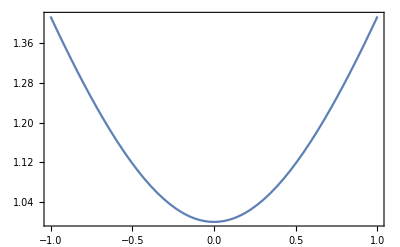

```mathematica
With[{m=1},Plot[√(p^2+m^2),{p,-1,1},Frame->True]]
```

```mathematica
FunctionConvexity[√(p^2+m^2),p]
```

ConditionalExpression[1, m∈ℝ]

The Hamiltonian is indeed convex for m>0

```mathematica
FullSimplify[legendreTransform[√(#^2+m^2)&][p,v],{m,v}∈Reals]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-(m v^2)/(√(1-v^2))-√(1/(1-v^2)) Abs[m]

Hmm, our function seems to struggle a bit

So let’s do this one by hand

First, we define the velocity as the derivative of our Hamiltonian

```mathematica
v==D[√(p^2+m^2),p]
```

v==p/(√(m^2+p^2))

And re-arrange for the momentum

```mathematica
Solve[v==p/(√(m^2+p^2)),p]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{p→-(m v)/(√(1-v^2))},{p→(m v)/(√(1-v^2))}}

Aha, here’s the culprit! 
Two branches - we’ll pick the positive one

We now use our definition for the Legendre transform

```mathematica
With[{p=(m v)/(√(1-v^2))},
Simplify[p v - √(m^2+p^2),{m>0,v^2<1}]
]
```

-m √(1-v^2)

Which indeed is the Lagrangian for a relativistic particle!

Coincidentally, this is one example where the L = T - V intuition breaks down

## Lagrange Multipliers

...